```mathematica
pdf[g_,gm_,kappa_,mu_,N_,m_]:= (mu(1+kappa)^((mu +1)/2)Exp[-mu(1+kappa)g/10^((N/m gm)/10)] g^((mu-1)/2))/(kappa^((mu -1)/2)Exp[mu kappa](10^((N/m gm)/10))^((mu+1)/2))BesselI[mu -1,2 mu √(kappa (kappa+1)g/10^((N/m gm)/10))];
```

```mathematica
probError[g_,alfa_]:=1/2 Exp[-alfa g];
```

```mathematica
BER[gm_,kappa_,mu_,alfa_,N_,m_]:=Re[NIntegrate[probError[g,alfa]×pdf[g,gm,kappa,mu,N,m],{g,0,∞}]];
```

```mathematica
PNm[gm_,kappa_,mu_,alfa_,k_,N_,m_]:=((N!)/(m!(N-m)!))×(1-BER[gm,kappa,mu,alfa,k,N])^(N-m)×(BER[gm,kappa,mu,alfa,k,N])^m;
PeM[gm_,kappa_,mu_,alfa_,k_,N_,t_] := 1 - Sum[PNm[gm,kappa,mu,alfa,k,N,m],{m,0,t}];
```

```mathematica
PeM[1,2,1,0.5,12,12,0]
```

0.984177

FSK, Golay -> N = 23, k = 12, t = 3, kappa = 2

```mathematica
LogPlot[{PeM[x,2,1,0.5,12,23,3],PeM[x,2,2,0.5,12,23,3],PeM[x,2,3,0.5,12,23,3],PeM[x,2,4,0.5,12,23,3]},{x,-10,30},AxesLabel->{"γm(dB)","Error Message Probability"},PlotRange->{10^-4,1},PlotLegends->{"μ=1","μ=2","μ=3","μ=4"}, PlotStyle->{Blue,Red,Green,Black}]
```

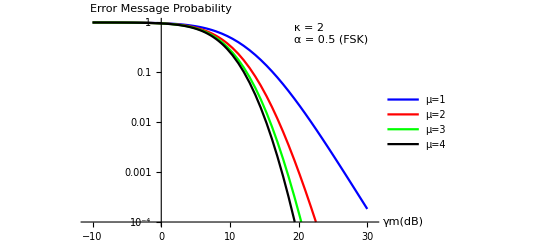

```mathematica
LogPlot[{PeM[x,2,1,1,12,23,3],PeM[x,2,2,1,12,23,3],PeM[x,2,3,1,12,23,3],PeM[x,2,4,1,12,23,3]},{x,-10,30},AxesLabel->{"γm(dB)","Error Message Probability"},PlotRange->{10^-4,1},PlotLegends->{"μ=1","μ=2","μ=3","μ=4"}, PlotStyle->{Blue,Red,Green,Black}]
```

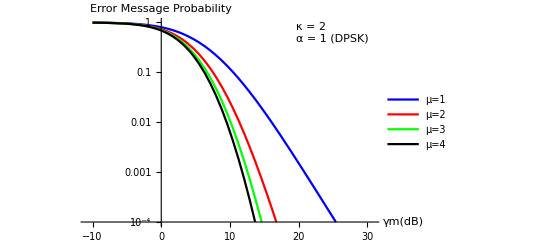

```mathematica
LogPlot[{PeM[x,0.0001,2,0.5,12,23,3],PeM[x,1,2,0.5,12,23,3],PeM[x,2,2,0.5,12,23,3],PeM[x,3,2,0.5,12,23,3]},{x,-10,30},AxesLabel->{"γm(dB)","Error Message Probability"},PlotRange->{10^-4,1},PlotLegends->{"κ→0","κ=1","κ=2","κ=3"}, PlotStyle->{Blue,Red,Green,Black}]
```

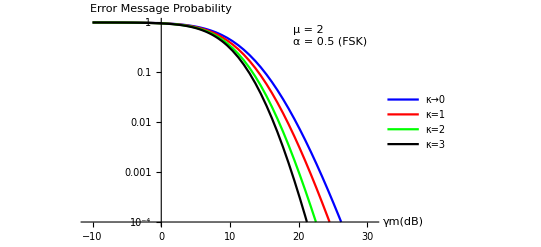

```mathematica
LogPlot[{PeM[x,0.0001,2,1,12,23,3],PeM[x,1,2,1,12,23,3],PeM[x,2,2,1,12,23,3],PeM[x,3,2,1,12,23,3]},{x,-10,30},AxesLabel->{"γm(dB)","Error Message Probability"},PlotRange->{10^-4,1},PlotLegends->{"κ→0","κ=1","κ=2","κ=3"}, PlotStyle->{Blue,Red,Green,Black}]
```